## Population genetic recursions

### Haploid model of selection

#### Reference

p	-- proportion (frequency) of allele A
p_t	-- p at time t. Can also be written as p(t)
pup	-- “p update,” the update function for p 
wA 	-- fitness of genotype A  
wa 	-- fitness of genotype a

Below is the “p update” function. It takes in a p and outputs the p for the next timestep. This function is essentially our p(t+1) = (p(t) W)/(p(t) W + (1- p(t)))function from class, where W = wA/wa.

```mathematica
pup[p_]:=p (wA/wa)/(p (wA/wa)+(1-p))
```

We can use Mathematica to show how applying the recursion twice can be simplified.

```mathematica
pup[p0]
```

(p0 wA)/(wa (1-p0+(p0 wA)/wa))

```mathematica
pup[pup[p0]]
```

(p0 wA^2)/(wa^2 (1-p0+(p0 wA)/wa) (1-(p0 wA)/(wa (1-p0+(p0 wA)/wa))+(p0 wA^2)/(wa^2 (1-p0+(p0 wA)/wa))))

```mathematica
Simplify[pup[pup[p0]]]
```

```mathematica
(p0 wA^2)/(-(-1+p0) wa^2+p0 wA^2)==(p0 wA^2)/((1-p0) wa^2+p0 wA^2)==(p0 (wA/wa)^2)/((1-p0) 1+p0 (wA/wa)^2)
```

```mathematica
p[t_]:=(p0 (wA/wa)^t)/((1-p0) 1+p0 (wA/wa)^t)
```

If wA > wa

```mathematica
p[infinity] == (p0 (wA/wa)^t)/(p0 (wA/wa)^t) == 1
```

If wA < wa

```mathematica
p[infinity] ==0/((1-p0) 1+0) ==0
```

We are also interested in how p changes in each generation, in the book this is referred to as a difference equation:

```mathematica
(pup[p]-p)==p(1-p)((wA/wa)-1)/(p (wA/wa)+(1-p))
```

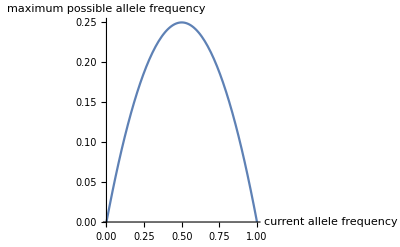

```mathematica
Plot[p(1-p),{p,0,1}, AxesLabel->{"current allele frequency","maximum possible allele frequency"}]
```

We redefine pup in order to make the function take fitness parameters as input as well.

```mathematica
pup[p_,wA_,wa_]:=p (wA/wa)/(p (wA/wa)+(1-p))
```

Now we plot the change in allele frequency as a function of current frequency.

```mathematica
Manipulate[Plot[pup[p,wA,wa]-p,{p,0,1},PlotRange->{-.2,.2},Frame->True,FrameLabel->{"current allele frequency","change in allele frequency"}],{{wA,1},0,2},{{wa,1},0,2}]
```

We can also separate out the two parts of the equation to get

```mathematica
p*(1-p) (*genetic variation in the popultion*)
```

and

```mathematica
((wA/wa)-1)/(p (wA/wa)+(1-p))(*amount of fitness left to gain*)
```

We also calculated the frequency after t time units to give

```mathematica
pt[wA_,wa_,p0_,t_]:=(p0 (wA/wa)^t)/(-(-1+p0) +p0 (wA/wa)^t)
```

We will plot frequency over time starting with an initial frequency of 1%.

```mathematica
Manipulate[Plot[pt[wA,wa,0.01,t] ,{t,0,50},PlotRange->{{0,50},{0,1}},Frame->True,FrameLabel->{"Time (generation)","Frequency of A"}],{{wA,1},0,2},{{wa,1},0,2}]
```

#### After manipulating the plots, describe your own interpretation of how this model described haploid population genetic dynamics.